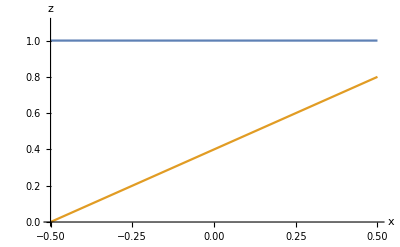

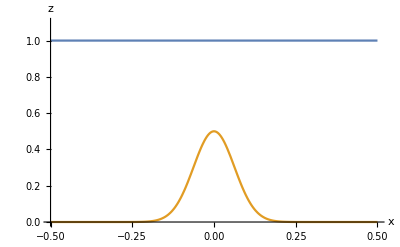

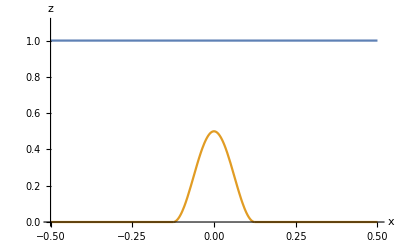

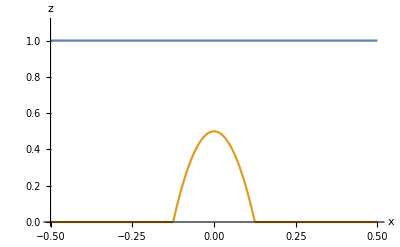

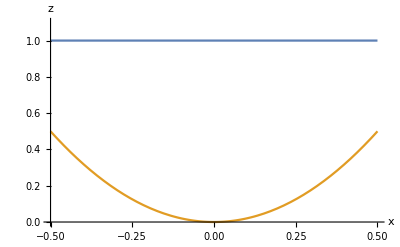

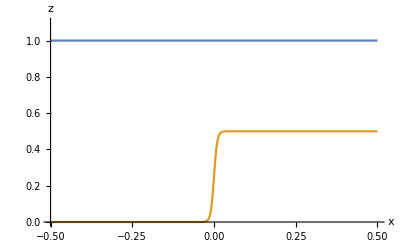

```mathematica
Plot[{1,0.4+0.8x},{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,z}]
Plot[{1,0.5Exp[-128x^2]},{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,z}]
Plot[{1,Piecewise[{{Cos[4Pi*x]^2/2,Abs@x<1/8}},0]},{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,z}]
Plot[{1,Piecewise[{{0.5-32x^2,Abs@x<0.125}},0]},{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,z}]
Plot[{1,2x^2},{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,z}]
Plot[{1,0.25(1+Tanh[100x])},{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,z}]
```

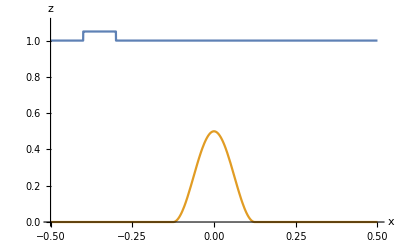

```mathematica
Plot[{Piecewise[{{1.05,-.4<x<-.3}},1],Piecewise[{{Cos[4Pi*x]^2/2,Abs@x<1/8}},0]},{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,z},Exclusions->None]
```

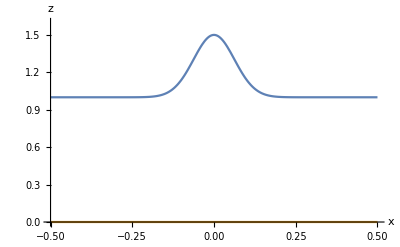

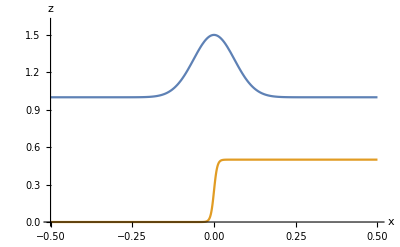

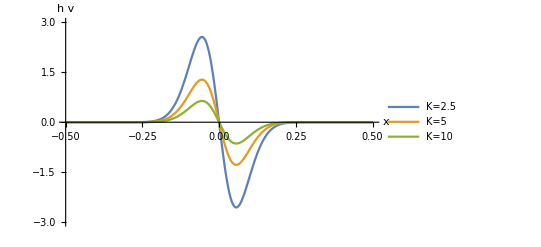

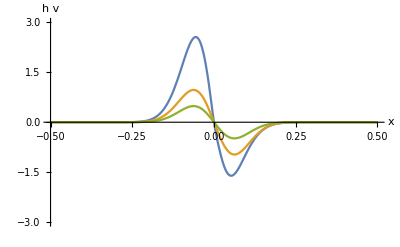

```mathematica
Plot[{1+0.5Exp[-128x^2],0},{x,-0.5,0.5},PlotRange->{0,1.6},AxesOrigin->{-0.5,0},AxesLabel->{x,z}]
Plot[{1+0.5Exp[-128x^2],0.25(1+Tanh[100x])},{x,-0.5,0.5},PlotRange->{0,1.6},AxesOrigin->{-0.5,0},AxesLabel->{x,z}]
Plot[{(1+0.5Exp[-128x^2])/2.5*D[0.5Exp[-128t^2],t]/.t->x,(1+0.5Exp[-128x^2])/5*D[0.5Exp[-128t^2],t]/.t->x,(1+0.5Exp[-128x^2])/10*D[0.5Exp[-128t^2],t]/.t->x},{x,-0.5,0.5},PlotRange->{-3,3},AxesOrigin->{-0.5,0},AxesLabel->{x,h v},PlotLegends->{"K=2.5","K=5","K=10"}]
Plot[{(1+0.5Exp[-128x^2]-0.25(1+Tanh[100x]))/2.5*D[0.5Exp[-128t^2],t]/.t->x,1/5*D[0.5Exp[-128t^2],t]/.t->x,1/10*D[0.5Exp[-128t^2],t]/.t->x},{x,-0.5,0.5},PlotRange->{-3,3},AxesOrigin->{-0.5,0},AxesLabel->{x,h v}]
```

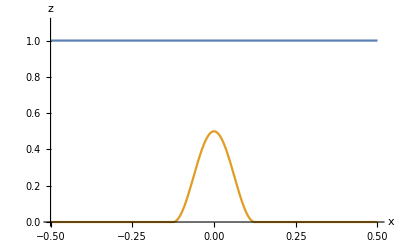

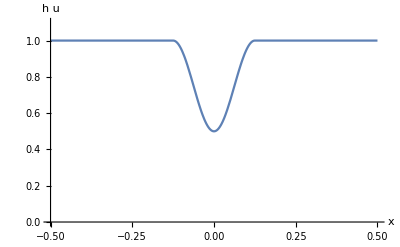

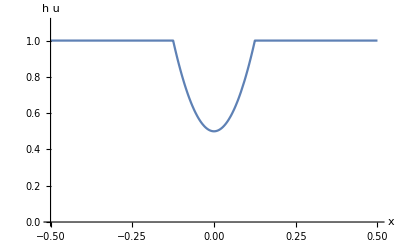

```mathematica
Plot[{1,Piecewise[{{Cos[4Pi*x]^2/2,Abs@x<1/8}},0]},{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,z},Exclusions->None]
Plot[(1-Piecewise[{{Cos[4Pi*x]^2/2,Abs@x<1/8}},0]),{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,h u},Exclusions->None]
Plot[(1-Piecewise[{{0.5-32x^2,Abs@x<0.125}},0]),{x,-0.5,0.5},PlotRange->{0,1.1},AxesOrigin->{-0.5,0},AxesLabel->{x,h u},Exclusions->None]
```